## Exoplanetas

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/michel/Library/CloudStorage/OneDrive-uv.cl/cursos/pregrado/Estadisticas/2024/Clases

```mathematica
exopl=Import["exoplanetas-11-2024.csv"];
```

```mathematica
header=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_measurement_type,radius_measurement_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
masas=Select[exopl[[All,3]],NumberQ];
```

```mathematica
Length@masas
```

4386

```mathematica
lg10masas=Log10@masas;
```

```mathematica
distmasas=SmoothKernelDistribution[Log10@masas];
```

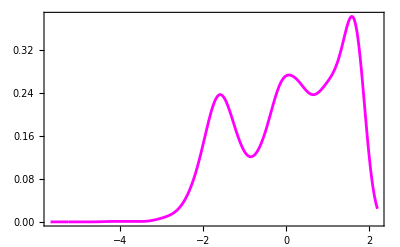

```mathematica
grma=Plot[PDF[distmasas,m],{m,-5.68,2.2},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
FindDistribution[Log10@masas]
```

MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}]

```mathematica
fdist=FindDistribution[Log10@masas,5]
```

{MixtureDistribution[{0.266876,0.464191,0.268933},{NormalDistribution[-1.54588,0.53526],NormalDistribution[0.317156,0.541194],NormalDistribution[1.52709,0.216679]}],MixtureDistribution[{0.143155,0.532003,0.324841},{NormalDistribution[-1.5713,0.245506],NormalDistribution[0.710644,0.723507],UniformDistribution[{-4.28793,1.95038}]}],NormalDistribution[0.117122,1.25613],StudentTDistribution[0.146324,1.22999,4771.72],LogisticDistribution[0.223105,0.732639]}

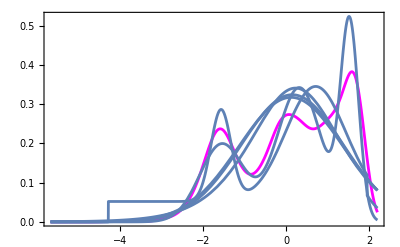

```mathematica
Show[grma,Plot[Table[PDF[fdist[[k]],lgm],{k,5}],{lgm,-5.68,2.2}],PlotRange->All]
```

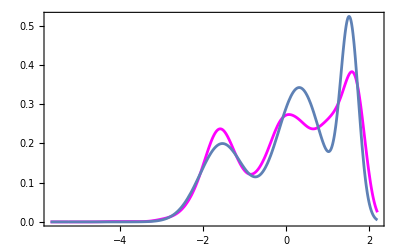

```mathematica
Show[grma,Plot[PDF[fdist[[1]],lgm],{lgm,-5.68,2.2}],PlotRange->All]
```

## Modelo de distribucion de masas de exoplanetas, Trimodal

```mathematica
modelo=MixtureDistribution[{a1,a2,a3},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3]}];
```

```mathematica
PDF[modelo,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3) √(2 π) σ3)

```mathematica
Integrate[(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3) √(2 π) σ1),{x,-∞,∞},Assumptions->σ1>0]
```

a1/(a1+a2+a3)

```mathematica
mincuad=Sum[(PDF[distmasas,lg10masas[[k]]]-PDF[modelo,lg10masas[[k]]])^2,{k,Length@lg10masas}];
```

```mathematica
paramini={{a1,0.3},{a2,0.4},{a3,0.6},{μ1,-1.5},{σ1,.7},{μ2,.5},{σ2,.6},{μ3,1.5},{σ3,.8}};
```

```mathematica
paraminiT=Thread[paramini[[All,1]]->paramini[[All,2]]]
```

```mathematica
{a1->0.3,a2->0.3,a3->0.4,μ1->-1.56,σ1->0.7,μ2->0.25,σ2->0.1,μ3->1.8,σ3->0.1}
```

{a1→0.3,a2→0.3,a3→0.4,μ1→-1.56,σ1→0.7,μ2→0.25,σ2→0.1,μ3→1.8,σ3→0.1}

```mathematica
Plot[PDF[modelo,x]/.paraminiT,{x,-5,3}];
```

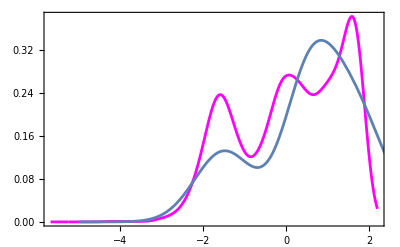

```mathematica
Show[grma,%]
```

```mathematica
AbsoluteTiming[sol=NMinimize[mincuad,{{a1,0.,1.},{a2,0.,1.},{a3,0.,1.},{μ1,-2.,-1.},{σ1,.5,1.5},{μ2,.3,.6},{σ2,.2,.8},{μ3,1.,2.},{σ3,.2,.9}},Method->"SimulatedAnnealing"]]
```

{13.4014,{0.506499,{a1→0.279526,a2→0.695533,a3→0.389789,μ1→-1.62726,σ1→0.368563,μ2→0.221376,σ2→0.75049,μ3→1.58718,σ3→0.355304}}}

```mathematica
sol[[2]]
```

{a1→0.279526,a2→0.695533,a3→0.389789,μ1→-1.62726,σ1→0.368563,μ2→0.221376,σ2→0.75049,μ3→1.58718,σ3→0.355304}

```mathematica
modelo/.sol[[2]]
```

MixtureDistribution[{0.585449,0.858669,0.490827},{NormalDistribution[-1.57957,0.427342],NormalDistribution[0.00149188,0.489691],NormalDistribution[1.17441,0.539763]}]

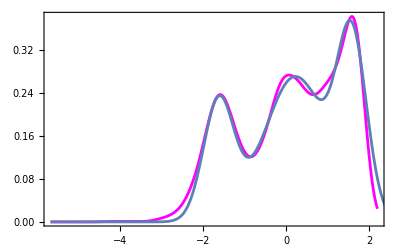

```mathematica
grOLS=Show[grma,Plot[PDF[modelo/.sol[[2]],lgm],{lgm,-5.68,2.5}]]
```

```mathematica
masasT=masas/0.003146;
```

```mathematica
distmasasT=SmoothKernelDistribution[Log10@masasT];
```

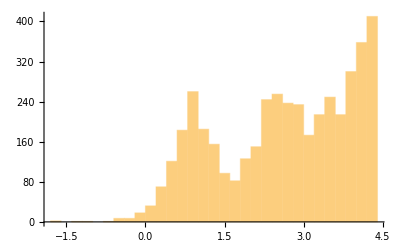

```mathematica
Histogram[Log10@masasT]
```

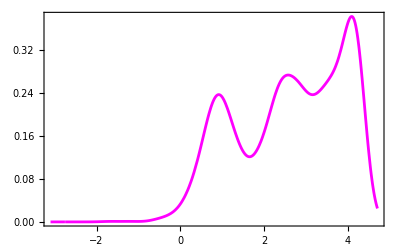

```mathematica
grmaT=Plot[PDF[distmasasT,m],{m,-3.1,4.7},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
PDF[modelo/.sol[[2]],x]
```

0.320667 ⅇ^(-3.96067 (-1.58718+x)^2)+0.270894 ⅇ^(-0.887729 (-0.221376+x)^2)+0.221685 ⅇ^(-3.68083 (1.62726+x)^2)

```mathematica
NIntegrate[PDF[modelo/.sol[[2]],x],{x,-10,10}]
```

1.

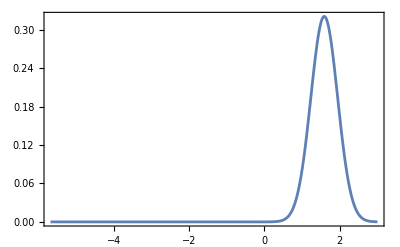
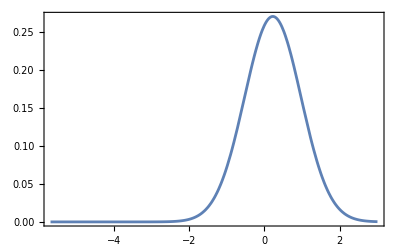
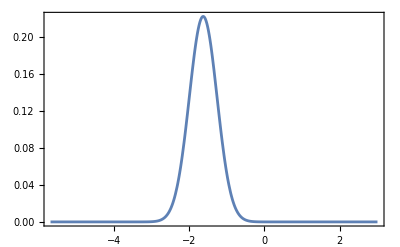

```mathematica
Table[Plot[PDF[modelo/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,Frame->True,Axes->False],{k,3}]
```

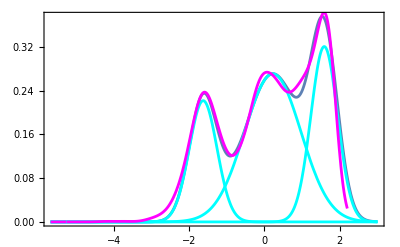

```mathematica
Show[Plot[PDF[modelo/.sol[[2]],lgm],{lgm,-5.68,3},Frame->True],Table[Plot[PDF[modelo/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,PlotStyle->Cyan],{k,3}],grma]
```

## Modelo de distribucion de masas de exoplanetas, Tetramodal

```mathematica
modelo4=MixtureDistribution[{a1,a2,a3,a4},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3],NormalDistribution[μ4,σ4]}];
```

```mathematica
PDF[modelo4,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3+a4) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3+a4) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3+a4) √(2 π) σ3)+(a4 ⅇ^(-(x-μ4)^2/(2 σ4^2)))/((a1+a2+a3+a4) √(2 π) σ4)

```mathematica
mincuad=Sum[(PDF[distmasas,lg10masas[[k]]]-PDF[modelo4,lg10masas[[k]]])^2,{k,Length@lg10masas}];
```

```mathematica
AbsoluteTiming[sol=NMinimize[mincuad,{{a1,0.,1.},{a2,0.,1.},{a3,0.,1.},{a4,0.,1.},{μ1,-2.,-1.},{σ1,.5,1.5},{μ2,.3,.6},{σ2,.2,.8},{μ3,1.,2.},{σ3,.2,.9},{μ4,-1.,2.},{σ4,.2,.9}},Method->"SimulatedAnnealing"]]
```

{15.1691,{0.0110774,{a1→0.660317,a2→0.71121,a3→0.333331,a4→0.940684,μ1→-1.59546,σ1→0.428428,μ2→1.23595,σ2→0.448939,μ3→1.66824,σ3→0.232028,μ4→0.0310708,σ4→0.531072}}}

```mathematica
sol[[2]]
```

{a1→0.660317,a2→0.71121,a3→0.333331,a4→0.940684,μ1→-1.59546,σ1→0.428428,μ2→1.23595,σ2→0.448939,μ3→1.66824,σ3→0.232028,μ4→0.0310708,σ4→0.531072}

```mathematica
modelo4/.sol[[2]]
```

MixtureDistribution[{0.660317,0.71121,0.333331,0.940684},{NormalDistribution[-1.59546,0.428428],NormalDistribution[1.23595,0.448939],NormalDistribution[1.66824,0.232028],NormalDistribution[0.0310708,0.531072]}]

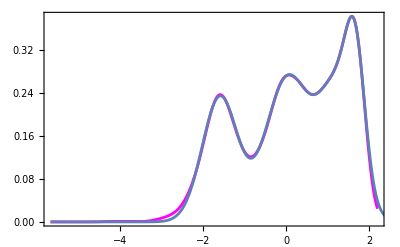

```mathematica
grOLS=Show[grma,Plot[PDF[modelo4/.sol[[2]],lgm],{lgm,-5.68,2.5}]]
```

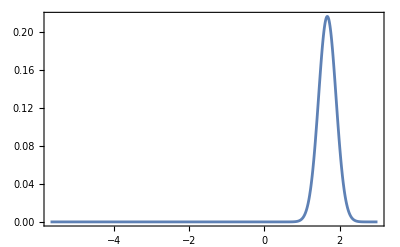
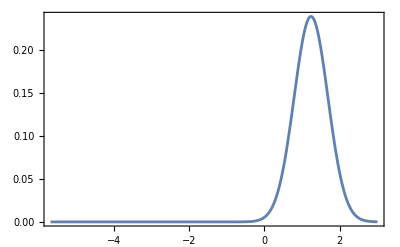
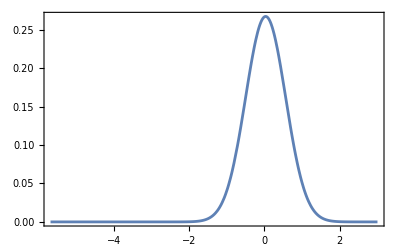
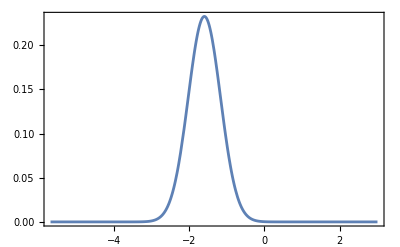

```mathematica
Table[Plot[PDF[modelo4/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,Frame->True,Axes->False],{k,4}]
```

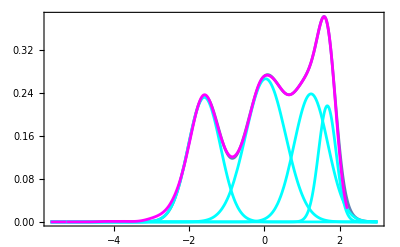

```mathematica
Show[Plot[PDF[modelo4/.sol[[2]],lgm],{lgm,-5.68,3},Frame->True],Table[Plot[PDF[modelo4/.sol[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,PlotStyle->Cyan],{k,4}],grma]
```

## Maximum Likelihood Estimator

```mathematica
modelo4=MixtureDistribution[{a1,a2,a3,a4},{NormalDistribution[μ1,σ1],NormalDistribution[μ2,σ2],NormalDistribution[μ3,σ3],NormalDistribution[μ4,σ4]}];
```

```mathematica
PDF[modelo4,x]
```

(a1 ⅇ^(-(x-μ1)^2/(2 σ1^2)))/((a1+a2+a3+a4) √(2 π) σ1)+(a2 ⅇ^(-(x-μ2)^2/(2 σ2^2)))/((a1+a2+a3+a4) √(2 π) σ2)+(a3 ⅇ^(-(x-μ3)^2/(2 σ3^2)))/((a1+a2+a3+a4) √(2 π) σ3)+(a4 ⅇ^(-(x-μ4)^2/(2 σ4^2)))/((a1+a2+a3+a4) √(2 π) σ4)

```mathematica
loglk=LogLikelihood[modelo4,Log10@masas];
```

```mathematica
AbsoluteTiming[sol0=NMaximize[
{loglk,a1>0&&a2>0&&a3>0&&σ1>0&&σ2>0&&σ3>0},{{a1,0.1,1.},{a2,0.1,1.},{a3,0.1,1.},{μ1,-2.,-1.5},{σ1,.2,.7},{μ2,-.5,.5},{σ2,.2,.9},{μ3,1.,2.},{σ3,.2,.9}}]]
```

{40.6294,{-4360.69,{a1→0.912204,a2→1.19695,a3→0.517614,μ1→-1.53623,σ1→0.534258,μ2→0.0969365,σ2→0.428354,μ3→1.24605,σ3→0.348639}}}

```mathematica
SeedRandom[IntegerPart@AbsoluteTime[]]
```

RandomGeneratorState[…]

```mathematica
AbsoluteTiming[sol1=NMaximize[{loglk, a1>0,a2>0,a3>0,a4>0,σ1>0,σ2>0,σ3>0,σ4>0},{{a1,0.,1.},{a2,0.,1.},{a3,0.,1.},{a4,0.,1.},{μ1,-2.,-1.},{σ1,.5,1.5},{μ2,.3,.6},{σ2,.2,.8},{μ3,1.,2.},{σ3,.2,.9},{μ4,-1.,2.},{σ4,.2,.9}},Method->"DifferentialEvolution"]]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a1,a2,a3,a4,μ1,μ2,μ3,μ4,σ1,σ2,σ3,σ4} = {0.524239,0.746442,1.32808,1.02614,«4»,0.,0.699846,0.112408,1.30538}.

{111.615,{-6317.77,{a1→1.17026,a2→2.16282,a3→1.14663,a4→0.509932,μ1→-1.58209,σ1→0.5186,μ2→0.411449,σ2→0.564132,μ3→1.57382,σ3→0.173917,μ4→-0.661982,σ4→0.936295}}}

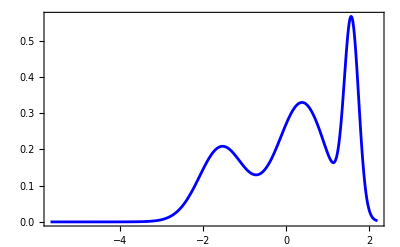

```mathematica
grMLE=Show[Plot[PDF[modelo4/.sol1[[2]],lgm],{lgm,-5.68,2.2},PlotStyle->Blue,Frame->True,Axes->False],PlotRange->All]
```

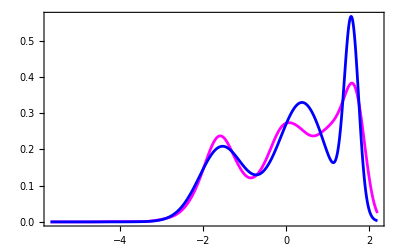

```mathematica
Show[grma,grMLE,PlotRange->All]
```

General::munfl: Exp[-869.755] is too small to represent as a normalized machine number; precision may be lost.

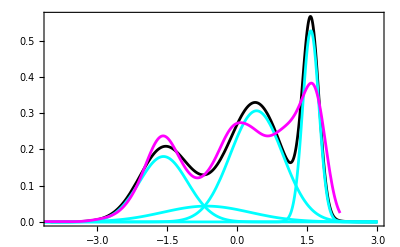

```mathematica
Show[Plot[PDF[modelo4/.sol1[[2]],lgm],{lgm,-4,3},Frame->True,PlotStyle->Black],Table[Plot[PDF[modelo4/.sol1[[2]],x][[k]]/.x->lgm,{lgm,-5.68,3},PlotRange->All,PlotStyle->Cyan],{k,4}],grma]
```

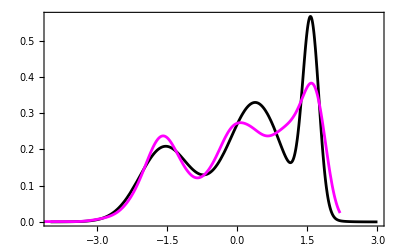

```mathematica
Show[Plot[PDF[modelo4/.sol1[[2]],lgm],{lgm,-4,3},Frame->True,PlotStyle->Black],grma]
```

```mathematica
{sol[[2]],sol1[[2]]}ᵀ//TableForm
```

a1→0.660317 | a1→1.17026
a2→0.71121 | a2→2.16282
a3→0.333331 | a3→1.14663
a4→0.940684 | a4→0.509932
μ1→-1.59546 | μ1→-1.58209
σ1→0.428428 | σ1→0.5186
μ2→1.23595 | μ2→0.411449
σ2→0.448939 | σ2→0.564132
μ3→1.66824 | μ3→1.57382
σ3→0.232028 | σ3→0.173917
μ4→0.0310708 | μ4→-0.661982
σ4→0.531072 | σ4→0.936295

```mathematica
a1/(a1+a2+a3+a4)/.sol[[2]]
```

0.249596

```mathematica
a1/(a1+a2+a3+a4)/.sol1[[2]]
```

0.234538

```mathematica
a2/(a1+a2+a3+a4)/.sol[[2]]
```

0.268833

```mathematica
a2/(a1+a2+a3+a4)/.sol1[[2]]
```

0.433461

```mathematica
a3/(a1+a2+a3+a4)/.sol[[2]]
```

0.125997

```mathematica
a3/(a1+a2+a3+a4)/.sol1[[2]]
```

0.229803

```mathematica
a4/(a1+a2+a3+a4)/.sol[[2]]
```

0.355573

```mathematica
a4/(a1+a2+a3+a4)/.sol1[[2]]
```

0.102198

## Relacion Masa Radio para exoplanetas

Calculos para reproducir resultados de https://arxiv.org/abs/2311.12593v2

```mathematica
Clear[exopl]
```

```mathematica
exopl=Import["exoplanetas-11-2024.csv"];
```

```mathematica
header=exopl[[1]]
```

{name,planet_status,mass,mass_error_min,mass_error_max,mass_sini,mass_sini_error_min,mass_sini_error_max,radius,radius_error_min,radius_error_max,orbital_period,orbital_period_error_min,orbital_period_error_max,semi_major_axis,semi_major_axis_error_min,semi_major_axis_error_max,eccentricity,eccentricity_error_min,eccentricity_error_max,inclination,inclination_error_min,inclination_error_max,angular_distance,discovered,updated,omega,omega_error_min,omega_error_max,tperi,tperi_error_min,tperi_error_max,tconj,tconj_error_min,tconj_error_max,tzero_tr,tzero_tr_error_min,tzero_tr_error_max,tzero_tr_sec,tzero_tr_sec_error_min,tzero_tr_sec_error_max,lambda_angle,lambda_angle_error_min,lambda_angle_error_max,impact_parameter,impact_parameter_error_min,impact_parameter_error_max,tzero_vr,tzero_vr_error_min,tzero_vr_error_max,k,k_error_min,k_error_max,temp_calculated,temp_calculated_error_min,temp_calculated_error_max,temp_measured,hot_point_lon,geometric_albedo,geometric_albedo_error_min,geometric_albedo_error_max,log_g,publication,detection_type,mass_measurement_type,radius_measurement_type,alternate_names,molecules,star_name,ra,dec,mag_v,mag_i,mag_j,mag_h,mag_k,star_distance,star_distance_error_min,star_distance_error_max,star_metallicity,star_metallicity_error_min,star_metallicity_error_max,star_mass,star_mass_error_min,star_mass_error_max,star_radius,star_radius_error_min,star_radius_error_max,star_sp_type,star_age,star_age_error_min,star_age_error_max,star_teff,star_teff_error_min,star_teff_error_max,star_detected_disc,star_magnetic_field,star_alternate_names}

```mathematica
header[[3]]
```

mass

```mathematica
header[[9]]
```

radius

```mathematica
{exopl[[All,3]],exopl[[All,9]]}ᵀ[[1;;10]]//TableForm
```

mass | radius
5.743 | 1.152
0.033 | 
9.866 | 
16.1284 | 
11.0873 | 
4.684 | 
8.5 | 
7.1 | 
1.64 |

```mathematica
datMR=Select[Rest@exopl,(NumberQ[#[[3]]]&& NumberQ[#[[9]]])&][[All,{9,3}]];
```

```mathematica
Length@datMR
```

2001

WolframAlphaQueryParseResults

```mathematica
masaJenT=1/0.003146
```

317.864

```mathematica
datMR[[All,2]]=masaJenT datMR[[All,2]];
```

```mathematica
bajaMR=Select[datMR,#[[2]]<= 4.4&];
```

```mathematica
Length@bajaMR
```

201

```mathematica
nlf=NonlinearModelFit[bajaMR,x^a,{a},x]
```

FittedModel[…]

```mathematica
Normal[nlf]
```

1/x^0.380275

```mathematica
lmf=Fit[Log10@bajaMR, {x},x]
```

-0.320011 x

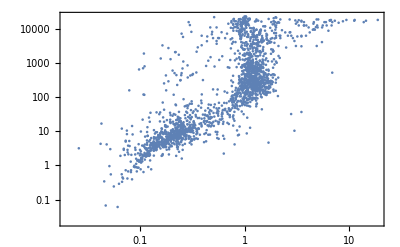

```mathematica
ListLogLogPlot[datMR,Frame->True]
```